```mathematica
SetDirectory[NotebookDirectory[]];
```

## Plotting

```mathematica
col={LightBlue,Yellow,Orange,Red,Darker[Red],Black};
Color[norm_]:=If[NumberQ[norm],If[norm==0,White,Blend[col,N@(1/Abs[(Log10[norm]-1)])]],LightGreen];
Color2D[val_]:=If[NumberQ[val],If[val==0,White,Blend[col,N@(1/Abs[(Log10[val]-1)])]],LightGreen];
Transparency[value_]:=If[value==0,0,(1/Abs[(Log10[value]-1)^3])];
Transparency2D[value_]:=If[value==0,0,(5/Abs[Log10[value]-1])];
(Color[#])&/@(N@Subdivide[34])
(Color2D[#])&/@(N@Subdivide[34])
(Transparency[#])&/@(N@Subdivide[34])
```

{GrayLevel[1],RGBColor[1., 0.5124349907993843, 0.],RGBColor[1., 0.3791494052887073, 0.],RGBColor[1., 0.28307460971835946, 0.],RGBColor[1., 0.204273101771057, 0.],RGBColor[1., 0.13575015506581195, 0.],RGBColor[1., 0.07413987839229591, 0.],RGBColor[1., 0.01753537172107439, 0.],RGBColor[0.9764934924882028, 0., 0.],RGBColor[0.9432993946673778, 0., 0.],RGBColor[0.9117273191814487, 0., 0.],RGBColor[0.8814964993271748, 0., 0.],RGBColor[0.8523932111484952, 0., 0.],RGBColor[0.8242505457154097, 0., 0.],RGBColor[0.7969353547271245, 0., 0.],RGBColor[0.7703394989279324, 0., 0.],RGBColor[0.7443737910746753, 0., 0.],RGBColor[0.7189636885995988, 0., 0.],RGBColor[0.694046158148909, 0., 0.],RGBColor[0.6695673462803309, 0., 0.],RGBColor[0.6242949690268034, 0., 0.],RGBColor[0.5768257382394131, 0., 0.],RGBColor[0.5299896126613525, 0., 0.],RGBColor[0.4837242263997059, 0., 0.],RGBColor[0.43797423938849045, 0., 0.],RGBColor[0.3926902652220303, 0., 0.],RGBColor[0.34782799805268405, 0., 0.],RGBColor[0.30334749539893835, 0., 0.],RGBColor[0.25921258430677724, 0., 0.],RGBColor[0.2153903660184942, 0., 0.],RGBColor[0.1718507999864453, 0., 0.],RGBColor[0.1285663523073899, 0., 0.],RGBColor[0.08551169684813842, 0., 0.],RGBColor[0.042663459766269285, 0., 0.],RGBColor[0., 0., 0.]}

{GrayLevel[1],RGBColor[1., 0.5124349907993843, 0.],RGBColor[1., 0.3791494052887073, 0.],RGBColor[1., 0.28307460971835946, 0.],RGBColor[1., 0.204273101771057, 0.],RGBColor[1., 0.13575015506581195, 0.],RGBColor[1., 0.07413987839229591, 0.],RGBColor[1., 0.01753537172107439, 0.],RGBColor[0.9764934924882028, 0., 0.],RGBColor[0.9432993946673778, 0., 0.],RGBColor[0.9117273191814487, 0., 0.],RGBColor[0.8814964993271748, 0., 0.],RGBColor[0.8523932111484952, 0., 0.],RGBColor[0.8242505457154097, 0., 0.],RGBColor[0.7969353547271245, 0., 0.],RGBColor[0.7703394989279324, 0., 0.],RGBColor[0.7443737910746753, 0., 0.],RGBColor[0.7189636885995988, 0., 0.],RGBColor[0.694046158148909, 0., 0.],RGBColor[0.6695673462803309, 0., 0.],RGBColor[0.6242949690268034, 0., 0.],RGBColor[0.5768257382394131, 0., 0.],RGBColor[0.5299896126613525, 0., 0.],RGBColor[0.4837242263997059, 0., 0.],RGBColor[0.43797423938849045, 0., 0.],RGBColor[0.3926902652220303, 0., 0.],RGBColor[0.34782799805268405, 0., 0.],RGBColor[0.30334749539893835, 0., 0.],RGBColor[0.25921258430677724, 0., 0.],RGBColor[0.2153903660184942, 0., 0.],RGBColor[0.1718507999864453, 0., 0.],RGBColor[0.1285663523073899, 0., 0.],RGBColor[0.08551169684813842, 0., 0.],RGBColor[0.042663459766269285, 0., 0.],RGBColor[0., 0., 0.]}

{0,0.061642,0.0901204,0.115338,0.139226,0.162503,0.185529,0.208513,0.231593,0.254865,0.278399,0.30225,0.326462,0.351074,0.376115,0.401615,0.427597,0.454086,0.481102,0.508666,0.536796,0.565511,0.59483,0.624769,0.655347,0.686579,0.718484,0.751079,0.78438,0.818405,0.853171,0.888696,0.924997,0.962092,1.}

```mathematica
GRID[data_,opts__]:=Grid[data,opts,Spacings->{0,0},BaseStyle->ImageSizeMultipliers->1];
Prob1D[data_,rng_,norm_:None,opts___]:=ListLinePlot[data,opts,DataRange->rng,
Epilog->Inset[Round[Log10@norm,0.01],Scaled[{0.95,0.95}],Scaled[{1,1}]],
PlotRangePadding->0,Frame->True,FrameLabel->HoldForm@Abs[ψ]^2];
Phase1D[data_,rng_,opts___]:=ListLinePlot[data,opts,DataRange->rng,PlotRangePadding->0, Frame->True,FrameLabel->HoldForm@Arg[ψ],FrameTicks->{{{{-π,-π,0.1},{-π/2,-π/2,0.1},{0,0,0.1},{π/2,π/2,0.1},{π,π,0.1}},None},Automatic}];
Prob2D[data_,rng_,norm_:None,opts___]:=ListDensityPlot[data,opts,DataRange->{rng,rng},Epilog->Inset[Round[Log10@norm,0.01],Scaled[{0.95,0.95}],Scaled[{1,1}]],ColorFunction->(Opacity [(*Transparency2D[*)#,Color[norm]]&),ColorFunctionScaling->True,(*OpacityFunction->Transparency,OpacityFunctionScaling->True,*)PlotRangePadding->0,InterpolationOrder->0];
Phase2D[data_,rng_,opts___]:=ListDensityPlot[data,opts,DataRange->{rng,rng},PlotRangePadding->0,ColorFunction->Hue];
(*3D plots, colors: indicate total norm- transparency: local values*)
Prob3D[data_,rng_,norm_:None,opts___]:=ListDensityPlot3D[data,opts,
DataRange->{rng,rng,rng},
Epilog->Inset[If[norm==0.0,"-∞",Round[Log10@norm,0.01]],Scaled[{0.95,0.95}],Scaled[{1,1}]],
ColorFunction->(Color[norm]&),ColorFunctionScaling->False,
OpacityFunction->Transparency,OpacityFunctionScaling->True,
PlotRangePadding->0];
Phase3D[data_,rng_,opts___]:=ListDensityPlot3D[data,opts,DataRange->{rng,rng,rng},PlotRangePadding->0,RegionFunction->Function[{x,y,z},x^2+y^2+z^2≤(Last@rng)^2/√2],OpacityFunction->Function[f,0.05],ColorFunction->Hue];
```

```mathematica
(*
PlotLegends->BarLegend[Automatic,LegendLayout->"Column",LegendMarkerSize->{10,1.04size},LegendMargins->{{-15,0},{3,0}}],
OpacityFunction->Function[f,f],
ColorFunction->"SunsetColors",
PlotLegends->BarLegend[Automatic,LegendLayout->"Column"(*,LegendMarkerSize->{10,1.04size},LegendMargins->{{-15,0},{3,If[top,35,0]}}*)],FrameTicks->{{All,None},{All,All}},PlotRangePadding->0*)
(*PlotLegends->BarLegend[Automatic,LegendLayout->"Column",LegendMarkerSize->{10,1.04size},LegendMargins->{{-15,0},{3,0}}]*)
(*PlotLegends->BarLegend[Automatic,LegendLayout->"Column",LegendMarkerSize->{10,1.04size},LegendMargins->{{-15,0},{3,0}}],*)
```

## Text

```mathematica
Hs:=StringSplit[#,"_"][[-2]]&;
S[li_]:=SortBy[li,StringCount[Hs[#],DigitCharacter]&];
```

```mathematica
dir="~/Projects/Quantum/TDSE/projects/template/Results/";
psis=S@FileNames[dir<>"psi*.dat"]
moms=S@FileNames[dir<>"mom*.dat"];
pots=S@FileNames[dir<>"pot*.dat"];
```

```mathematica
ImportAndEchoNorm[file_]:=Block[{dat},dat=DeleteCases[Import[file],{}];
Echo[N[Total@dat[[All,-1]],10],FileBaseName[file]<>": "];
];
ImportAndGetNorm[file_]:=Block[{dat},dat=DeleteCases[Import[file],{}];
N[Total@dat[[All,-1]],10]
];
ImportAndPlot[file_]:=Block[{dat,base},dat=DeleteCases[Import[file],{}];
base=FileBaseName[file];
Switch[StringTake[base,-1],
"x",ListLinePlot[dat,PlotLabel->base,PlotRange->Full,Frame->True, FrameLabel->{x}],
"y",ListDensityPlot[dat,PlotLabel->base,ScalingFunctions->"Log",PlotRange->Full,AxesLabel->{x,y}(*,PlotLegends->Automatic*)],
"z",ListDensityPlot3D[dat,PlotLabel->base,PlotRange->Full,AxesLabel->{x,y,z},OpacityFunction->0.05,PlotLegends->Automatic]]
];
```

```mathematica
ImportAndEchoNorm/@psis;
ImportAndEchoNorm/@moms;
```

```mathematica
Multicolumn[ImportAndPlot/@psis,8]
```

```mathematica
Multicolumn[ImportAndPlot/@moms,3]
```

## Binary

```mathematica
DoubleQ[size_]:=size==8;
ReadBinaryWFHeader[st_]:=Join[BinaryReadList[st, "Integer32",3],BinaryReadList[st, "Real64",3]];
ReadBinaryWF[st_,dim_,n_,size_]:=Block[{typesize=If[DoubleQ[size],"Real64","Complex128"]},
Apply[Table[BinaryReadList[st, typesize,n],##]&,ConstantArray[n,dim-1]]
];
ImportBinaryAndPlot[file_,collapse_:False,scaleF_:Identity,opts___]:=Block[{dim,n,size,min,max,delta,st,
norm,dat,base,opt,rng,vLabel,ψ},
(*read*)
st=OpenRead[file,BinaryFormat->True];
{dim,n,size,min,max,delta}=ReadBinaryWFHeader[st];
dat=ReadBinaryWF[st,dim,n,size];
Close[file];

base=FileNameTake[file];
rng={min,max};

vLabel=Style[#,FontFamily->"Latin Modern Roman",14]&/@If[DoubleQ[size],(|ψ|)^2, {Abs[ψ],Arg[ψ]}];

dat=If[collapse,Abs[dat]^2,dat];
norm=Total[dat,∞];

dat=scaleF@dat;
Switch[dim,
1,If[DoubleQ[size]|| collapse,
Prob1D[dat,rng,opts],
GRID[{{Prob1D[Abs[dat]^2,rng,250,PlotStyle->Black],Phase1D[Arg@dat,rng,250,FrameStyle->Red,PlotStyle->Red]}}]],
2,If[DoubleQ[size]|| collapse,
Prob2D[dat,rng,norm,opts],
GRID[{{Prob2D[Abs[dat]^2,rng,250,True]},{Phase2D[Arg@dat,rng,250]}}]],
3,If[ DoubleQ[size]|| collapse,
Prob3D[dat,rng,norm,opts],
GRID[{{Prob3D[Abs[dat]^2,rng,250]},{Phase3D[Arg@dat,rng,250]}}]]
]
];
ImportBinaryWF[file_,collapse_:False]:=Block[{dim,n,size,min,max,delta,st,
norm,dat,base,opt,rng,vLabel,ψ},
(*read*)
st=OpenRead[file,BinaryFormat->True];
{dim,n,size,min,max,delta}=ReadBinaryWFHeader[st];
dat=ReadBinaryWF[st,dim,n,size];
dat=If[collapse,Abs[dat]^2,dat];
Close[file];
dat
];
```

```mathematica
Clear[p];
nam={"N","S_X", "S_Y", "S_Z", "D_XY","D_XZ","D_YZ","D_XYZ"};
dir="~/Projects/Quantum/QS/projects/template/Results/";
RemoveComments:=If[StringQ[#],ToExpression@StringTrim@StringReplace[#,RegularExpression["#.*"]->""],Identity[#]]&;
DisplayINI:=Dataset@Map[RemoveComments,Import[First@FileNames[#<>"../*.ini"]],-1]&;
dx=DisplayINI[dir]["DEFAULT","L"]/(DisplayINI[dir]["DEFAULT","n"]-1);
Echo[N@2π/DisplayINI[dir]["DEFAULT","L"],dp];
n=DisplayINI[dir]["DEFAULT","n"];
Echo[N@dx,"dx"];
Echo[n,"n"];
Echo[N@π/dx,Subscript[p, max]];
Id:=ToExpression@StringTake[#,-1]&;
viewpoints={{0,0,1},{1,0,0},{0,0,1}};
cplot:=ImportBinaryAndPlot[#,False,Identity,(*ClipPlanes->{{-1,1,-1,2}},OpacityFunction->None,*) 
PlotRange->Full,BoxStyle->{LightGray},Axes->True,InterpolationOrder->0,
ViewProjection->"Orthographic",
(*ViewMatrix->{T[s.rx.rz],p},*)
(*ViewVertical->viewpoints[[If[Id@#>3,1,Mod[Id@#,3,1]]]],*)
(*ViewPoint->({Top,Left,Front}[[Id@#]]),*)
(*ViewVector->{2.9If[Id@#>3,RotateRight[{0,30,0},Id@#],RotateLeft[{30,0.0,0.0},Id@#]],{0,0,0.0}},*)
AxesLabel->{Z,Y,X},PlotLabel->nam[[1+Id@#]]]&;

order:=ToExpression@StringExtract[#,"_"->-2,"i"->1]&;
```

dp  0.125664

dx  0.393701

n  128

p_max  7.97965

```mathematica
(*refresh*)
sorted:=SplitBy[SortBy[FileNames[dir<>#],order],order]&;
(*during*)
before=sorted@"RE3e3d*_bef_xyz.psib*";
selected=sorted@"RE3e3d*_*i_xyz.psib*";
after=sorted@"RE3e3d*_aft_xyz.psib*";
selected=Join[before,selected,after][[All]];
Grid[(cplot/@#)&/@selected,Spacings->-1]
```

```mathematica
Echo[(Total/@(( Total[ImportBinaryWF[#],∞]&/@#)&/@selected))[[All]],"Nowa wersja"]
```

Nowa wersja  {1.,1.,0.999957,0.97699,0.999717,1.00507,1.00924,0.987859,0.948832}

{1.,1.,0.999957,0.97699,0.999717,1.00507,1.00924,0.987859,0.948832}

```mathematica
nam={"N","S_X", "S_Y","D_XY"};
cplot:=ImportBinaryAndPlot[#,False,Identity,(*ClipPlanes->{{-1,1,-1,2}},OpacityFunction->None,*) 
PlotRange->Full,(*PlotLegends->Automatic, *)
FrameLabel->{Y,X},PlotLabel->nam[[1+ToExpression@StringTake[#,-1]]]]&;
order:=ToExpression@StringExtract[#,"_"->-2,"i"->1]&;
sorted:=SplitBy[SortBy[FileNames[dir<>#],order],order]&;
(*refresh*)
before=sorted@"RE2e2d*_bef_xy.psib*";
selected=sorted@"RE2e2d*_*i_xy.psib*";
after=sorted@"RE2e2d*_aft_xy.psib*";
selected=Join[before,selected,after][[All]];
Grid[(cplot/@#)&/@selected,Spacings->-1]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |

-Graphics-

-Graphics- | -Graphics- | -Graphics- | -Graphics- |  |  |  |

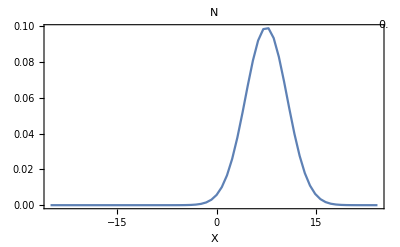
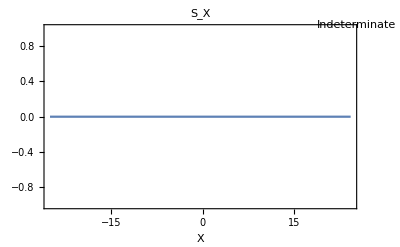
-Graphics- | -Graphics- |  |  |  |  |  |

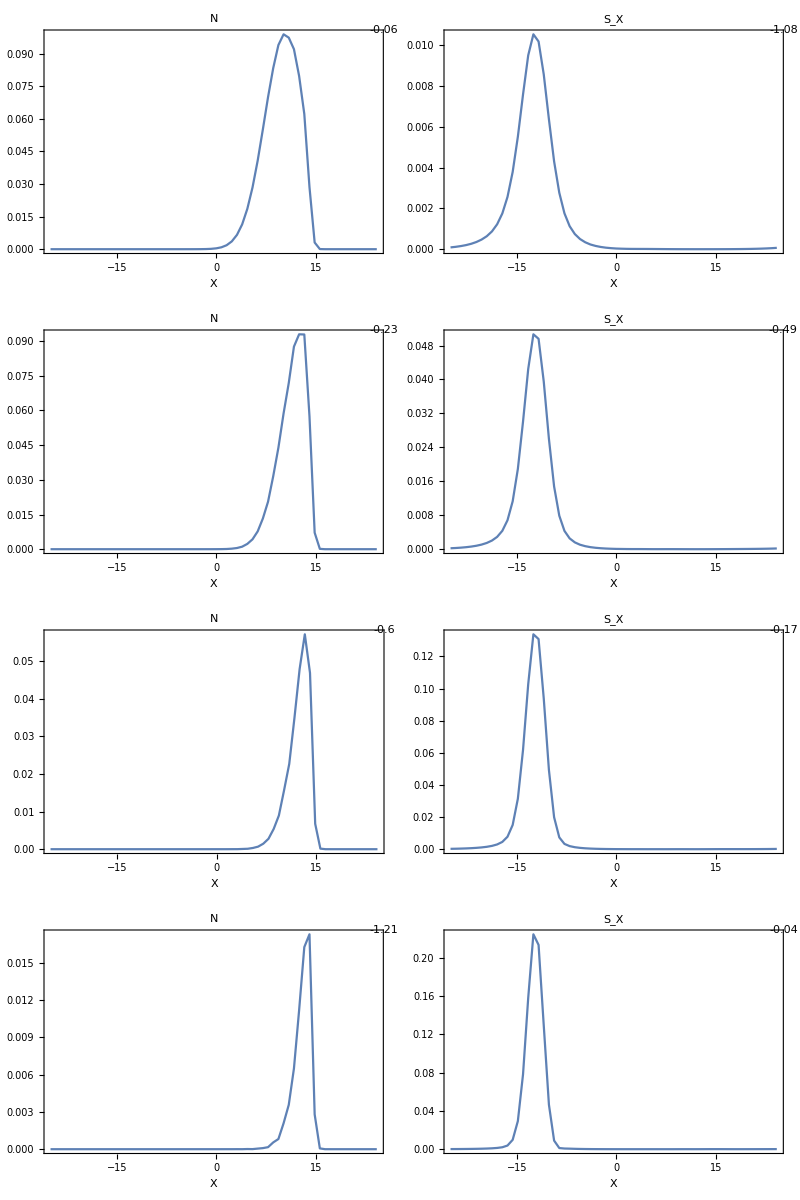

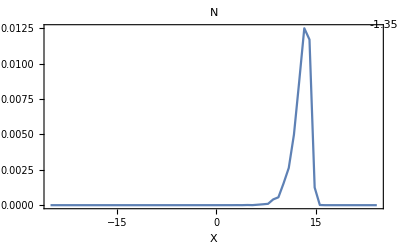
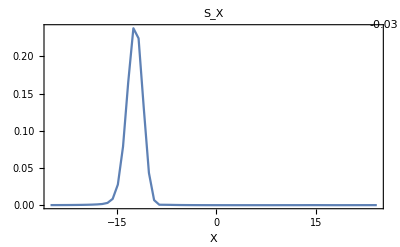
-Graphics- | -Graphics- |  |  |  |  |  |

```mathematica
nam={"N","S_X"};
cplot:=ImportBinaryAndPlot[#,False,Identity,(*ClipPlanes->{{-1,1,-1,2}},OpacityFunction->None,*) 
PlotRange->Full,(*PlotLegends->Automatic, *)
FrameLabel->{X},PlotLabel->nam[[1+ToExpression@StringTake[#,-1]]]]&;
order:=ToExpression@StringExtract[#,"_"->-2,"i"->1]&;
sorted:=SplitBy[SortBy[FileNames[dir<>#],order],order]&;
(*refresh*)
before=sorted@"RE1e1d*_bef_x.psib*";
selected=sorted@"RE1e1d*_*i_x.psib*";
after=sorted@"RE1e1d*_aft_x.psib*";
selected=Join[before,selected,after][[All]];
Grid[(cplot/@#)&/@selected,Spacings->-1]
```

## VG vs LG

```mathematica
dir="~/Projects/Quantum/QS/projects/template/Results/";
selected=FileNames[dir<>"RE1e2d*bef_x.psib"];
Multicolumn[ImportBinaryAndPlot[#,True,Identity,PlotRange->Full,FrameLabel->None, PlotLabel->StringDrop[FileBaseName[#],7]]&/@selected,6]
selected=FileNames[dir<>"RE1e2d*aft_x.psib"];
Multicolumn[ImportBinaryAndPlot[#,True,Identity,PlotRange->Full,FrameLabel->None, PlotLabel->StringDrop[FileBaseName[#],7]]&/@selected,6]
selected=FileNames[dir<>"RE1e2d*aft_x.momb"];
Multicolumn[ImportBinaryAndPlot[#,True,Identity,PlotRange->Full,FrameLabel->None, PlotLabel->StringDrop[FileBaseName[#],7]]&/@selected,6]
```

```mathematica
(*LG psib*)
selected=SortBy[FileNames[dir<>"RE1e1d_LG*i_x.psib"],ToExpression@StringExtract[#,"_"->-2,"i"->1]&];
Multicolumn[ImportBinaryAndPlot[#,True,Identity,PlotRange->Full,FrameLabel->None, PlotLabel->StringDrop[FileBaseName[#],7]]&/@selected,16]
(*LG momb*)
selected=SortBy[FileNames[dir<>"RE1e1d_LG*i_x.momb"],ToExpression@StringExtract[#,"_"->-2,"i"->1]&];
Multicolumn[ImportBinaryAndPlot[#,True,Identity,PlotRange->Full,FrameLabel->None, PlotLabel->StringDrop[FileBaseName[#],7]]&/@selected,12];
(*VG psib*)
selected=SortBy[FileNames[dir<>"RE1e1d_VG*i_x.psib"],ToExpression@StringExtract[#,"_"->-2,"i"->1]&];
Multicolumn[ImportBinaryAndPlot[#,True,Identity,PlotRange->Full,FrameLabel->None, PlotLabel->StringDrop[FileBaseName[#],7]]&/@selected,12]
(*VG momb*)
selected=SortBy[FileNames[dir<>"RE1e1d_VG*i_x.momb"],ToExpression@StringExtract[#,"_"->-2,"i"->1]&];
Multicolumn[ImportBinaryAndPlot[#,True,Identity,PlotRange->Full,FrameLabel->None, PlotLabel->StringDrop[FileBaseName[#],7]]&/@selected,12];
```

```mathematica
dir="~/Projects/Quantum/QS/projects/template/Results/";
(*LG psib*)
selected=SortBy[FileNames[dir<>"RE1e2d_LG*i_x.psib"],ToExpression@StringExtract[#,"_"->-2,"i"->1]&];
Multicolumn[ImportBinaryAndPlot[#,True,Identity,PlotRange->Full,FrameLabel->None, PlotLabel->StringDrop[FileBaseName[#],7]]&/@selected,16]
(*LG momb*)
selected=SortBy[FileNames[dir<>"RE1e2d_LG*i_x.momb"],ToExpression@StringExtract[#,"_"->-2,"i"->1]&];
Multicolumn[ImportBinaryAndPlot[#,True,Identity,PlotRange->Full,FrameLabel->None, PlotLabel->StringDrop[FileBaseName[#],7]]&/@selected,12];
(*VG psib*)
selected=SortBy[FileNames[dir<>"RE1e2d_VG*i_x.psib"],ToExpression@StringExtract[#,"_"->-2,"i"->1]&];
Multicolumn[ImportBinaryAndPlot[#,True,Identity,PlotRange->Full,FrameLabel->None, PlotLabel->StringDrop[FileBaseName[#],7]]&/@selected,12]
(*VG momb*)
selected=SortBy[FileNames[dir<>"RE1e2d_VG*i_x.momb"],ToExpression@StringExtract[#,"_"->-2,"i"->1]&];
Multicolumn[ImportBinaryAndPlot[#,True,Identity,PlotRange->Full,FrameLabel->None, PlotLabel->StringDrop[FileBaseName[#],7]]&/@selected,12];
```

```mathematica
dir="~/Projects/Quantum/QS/projects/template/Results/";
(*LG psib*)
selected=SortBy[FileNames[dir<>"RE1e3d_LG*i_x.psib"],ToExpression@StringExtract[#,"_"->-2,"i"->1]&];
Multicolumn[ImportBinaryAndPlot[#,True,Identity,PlotRange->Full,FrameLabel->None, PlotLabel->StringDrop[FileBaseName[#],7]]&/@selected,16]
(*LG momb*)
selected=SortBy[FileNames[dir<>"RE1e3d_LG*i_x.momb"],ToExpression@StringExtract[#,"_"->-2,"i"->1]&];
Multicolumn[ImportBinaryAndPlot[#,True,Identity,PlotRange->Full,FrameLabel->None, PlotLabel->StringDrop[FileBaseName[#],7]]&/@selected,12];
(*VG psib*)
selected=SortBy[FileNames[dir<>"RE1e3d_VG*i_x.psib"],ToExpression@StringExtract[#,"_"->-2,"i"->1]&];
Multicolumn[ImportBinaryAndPlot[#,True,Identity,PlotRange->Full,FrameLabel->None, PlotLabel->StringDrop[FileBaseName[#],7]]&/@selected,12]
(*VG momb*)
selected=SortBy[FileNames[dir<>"RE1e3d_VG*i_x.momb"],ToExpression@StringExtract[#,"_"->-2,"i"->1]&];
Multicolumn[ImportBinaryAndPlot[#,True,Identity,PlotRange->Full,FrameLabel->None, PlotLabel->StringDrop[FileBaseName[#],7]]&/@selected,12];
```

```mathematica
dir="~/Projects/Quantum/QS/projects/template/Results/";
extraction=KeySort/@KeySort @GroupBy[Select[FileNameTake/@FileNames[dir<>#],StringContainsQ[#,"_x"]&],{ToExpression@StringExtract[#,"_"->2,("CAP")->1]&,ToExpression@StringExtract[#,"_"->3,"i"->1]&},First]&;
psis=extraction@"RE*.psib";
moms=extraction@"RE*.momb";
style:=Style[#,16]&;
present:=TableForm[Table[Table[#2[#[i,j]],{j,Keys[#[i]]}],{i,Keys[#]}],TableHeadings->{style/@Keys[#],style/@Keys[#[[1]]]},TableAlignments->{Center, Center},TableSpacing->{0, 0}]&;
fun:=ImportBinaryAndPlot[dir<>#,True,Log10,PlotRange->{Full,{-12,0}},GridLines->Automatic,PlotLabel->#, FrameTicks->True,AspectRatio->1/2,ImageSize->300,FrameLabel->None]&;
present[psis,fun]
present[moms,fun]
```

```mathematica
dir="~/Projects/Quantum/QS/projects/template/Results/";
extraction=KeySort/@KeySort @GroupBy[Select[FileNameTake/@FileNames[dir<>#],StringContainsQ[#,"CAPK"]&&StringContainsQ[#,"_x"]&],{ToExpression@StringExtract[#,"_"->2,("CAPK")->1]&,ToExpression@StringExtract[#,"_"->3,"i"->1]&},First]&;
psis=extraction@"RE*.psib";
moms=extraction@"RE*.momb";
style:=Style[#,16]&;
present:=TableForm[Table[Table[#2[#[i,j]],{j,Keys[#[i]]}],{i,Keys[#]}],TableHeadings->{style/@Keys[#],style/@Keys[#[[1]]]},TableAlignments->{Center, Center},TableSpacing->{0, 0}]&;
fun:=ImportBinaryAndPlot[dir<>#,True,Log10,PlotRange->{Full,{-12,0}},GridLines->Automatic,PlotLabel->#, FrameTicks->True,AspectRatio->1/2,ImageSize->300,FrameLabel->None]&;
present[psis,fun]
present[moms,fun]
```

## Anims

```mathematica
ImportBinaryData[file_]:=Block[{dim,n,mode,columns, delta,dat,st,typesize,min,max},
st=OpenRead[file,BinaryFormat->True];
{dim,n,mode}=BinaryReadList[st, "Integer32",3];
{min,max,delta}=BinaryReadList[st, "Real64",3];
Partition[BinaryReadList[st, "Real64"],columns]
];
```

```mathematica
dir="~/Projects/Quantum/QS/projects/cap_benchmark/Results/";
fun:=ImportBinaryAndPlot[dir<>#,True,Identity,PlotRange->{Full,{0,.01}},GridLines->Automatic,PlotLabel->#, FrameTicks->True,AspectRatio->1/2,ImageSize->400,FrameLabel->None]&;
(*fun:=ImportBinaryAndPlot[dir<>#,True,Log10,PlotRange->{Full,{0,-12}},GridLines->Automatic,PlotLabel->#, FrameTicks->True,AspectRatio->1/2,ImageSize->300,FrameLabel->None]&;*)
LoadQ[name_:"RE*.psib"]:=Block[{psis},
psis=FileNameTake/@SortBy[FileNames[dir<>name],ToExpression@StringExtract[#,"_"->4(*,"i"-1*)]&];
Table[fun[psis[[i]]],{i,Length@psis}]
];
```

```mathematica
ShowEv[cap_]:=
Manipulate[
Grid[{{plot1[[i]],plot2[[i]]}}],
{i,1,Length[plot1],1},Initialization:>({plot1,plot2}={LoadQ[cap<>"psib"],LoadQ[cap<>"momb"]})]
```

```mathematica
ShowEv["RE*_20CAP0_*i_x."]
```

```mathematica
(*n=1024.;*)
(*n=4096;*)
n=1024;
L=100.;
(*dt=0.2;*)
(*dt=0.01;*)
dt=0.05;
dist=(0.8L);
dx=N@L/(n-1);
pmin=-π/dx;
pscale=2.0 *Pi*(n-1)/L/n;
dp=2π/n/dx;

FirstCollTime[pass_]:=Block[{},rel=0.1*pass *pmin;
time=dist/rel;
step=Abs@time/dt
]
```

```mathematica
GetFile[step_,cap_,pass_]:=First@FileNames[dir<>"RE*_"<>ToString[cap]<>"CAP"<>ToString[pass]<>"_"<>ToString[step]<>"i_*x.psib"];
```

```mathematica
FindNearest[cap_,pass_,fraction_:1]:=Block[{possibleTimes,collTime,near},
possibleTimes=ToExpression@StringExtract[#,"_"->4,"i"->1]&/@FileNames[dir<>"RE*_"<>ToString[cap]<>"CAP"<>ToString[pass]<>"_"<>"*x.psib"];
collTime=fraction*FirstCollTime[pass];
(*Echo[collTime,"Collision Time:"];*)
near=First@Nearest[possibleTimes,collTime];
{GetFile[near,cap,0],GetFile[near,cap,pass]}];
```

```mathematica
ProjectOut[res_,trash_]:=res-trash (Conjugate[trash].res);
AbsSq[res_]:=Total[Abs[res]^2];
```

```mathematica
Compare[cap_,pass_,fraction_:1]:=Block[{ref,test,res,res2,half},
{ref,test}=FindNearest[cap,pass,fraction];
refF=ImportBinary[ref];
testF=ImportBinary[test];
(*res=Abs@Total[Abs[testF]^2-Abs[refF]^2];*)
res=ProjectOut[testF,refF];
res=AbsSq[res]/AbsSq[refF];
(*momentum space*)
{ref,test}=StringReplace[#,"psib"->"momb"]&/@{ref,test};
refF=ImportBinary[ref];
testF=ImportBinary[test];
res2=ProjectOut[testF,refF];
(*res2=AbsSq[res2]/AbsSq[refF];*)
half=Length[res2]/2;
res2=AbsSq[res2[[2;;half+1]]]/AbsSq[res2[[half+1;;]]];
{res,res2}
];
```